zR[λ,w0] is the Rayleigh length of the beam. This corresponds to the distance it takes for the cross section area of the beam to double.
	w0 is the waist of the beam at its focus.
	λ is the wavelength of light (or wavelength / index of refraction if measuring in a medium)
w [λ,w0,z,z0] is the radius of the beam at a distance of (z - z0) from the waist
	z is the distance of where you are measuring from a reference point
	z0 is the distance of the waist from the same reference point
II[λ,I0,w0,x,y,z,z0] is the intensity profile of the beam
By default the wavelength is set to 1064 nm (note things are measured in meters)

```mathematica
zR[λ_,w0_]:=(π*w0^2)/λ;
w[λ_,w0_,z_,z0_]:=w0*√(1+((z-z0)/zR[λ,w0])^2);
II[λ_,I0_,w0_,x_,y_,z_,z0_]:=I0*(w0/w[λ,w0,z,z0])^2*Exp[(-2*(x^2+y^2))/(w[λ,w0,z,z0])^2];
λ=0.266*10^-6;
zR[λ,50*^-6]*1*^3
```

29.5262

```mathematica
(*calculate the diffraction limited spot diameter we would expect with an incoming beam diameter(diam) and a lens focal length(f) 
~assuming the incoming beam is smaller than the lens~
Outputs the diameter in um*)
θ0[λ_,diam_] := λ/(π*diam);
dw[θ0_,f_]:= 4*θ0 *f;
diam = 1*^-3;
f = 35*^-3;
θ = θ0[λ,diam];
dw[θ,f]*1*^6
```

11.8539

For entering data into the fitter:
JumpDistance corresponds to how much you move the knife edge (in meters) between each measurement
z_ is the distance of this measurement from your reference point (if converting from inch to m, the + 0.00000001 part is just to make sure 	Mathematica doesn’t break if you enter 0)
IIm1 is the list of your power measurements
It fits the points to an error function (the integral of a Gaussian) using the equation 1/2[1/2 π α w^2] ( erf((√2 (Y-Y0))/w)+1)+BG. Where the part in the brackets is the maximum power on the sensor.
It returns the fits of α: the amplitude of the Gaussian peak, w: the waist size at this z, Y0: the position of the knife when power is halved, and BG: the background illumination field (e.g. the sensor doesn’t measure 0 with no beam)

Enter the data for each position where you calculated the waist, be sure to edit references to JumpDistance, z and the fit outputs if adding new points in. Then run the beam profile fitter at the bottom

{4.58366×10^6,0.001,0.00002,32.11}

{α→1.55422×10^8,w→0.000319267,Y0→-0.000825466,BG→33.0389}

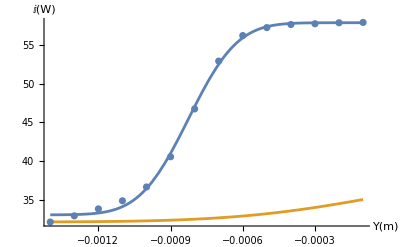

```mathematica
(*1st point*)
JumpDistance1=100*^-6;
z1=0+0.00000000000000000000000000001;
IIm1={57.96,57.92,57.79,57.69,57.29,56.26,52.95,46.76,40.56,36.65,34.86,33.81,32.91,32.11};
direction=Sign[IIm1[[1]]-IIm1[[Length[IIm1]]]];
Ym1=Range[Length[IIm1]]*JumpDistance1;
Data1=Table[0,{i,2},{j,Length[IIm1]}];
Data1[[1]]=-Ym1;
Data1[[2]]=IIm1;
model=1/4 π α w^2 ( direction*erf((√2 (Y-Y0))/w)+1)+BG;
{αGuess,wGuess,Y0Guess,BGGuess}={10*(0.3/0.5)^2/(0.001^2*1/4 π),0.001,0.00002,Min[IIm1]}
modelGuess=1/4 π αGuess wGuess^2 ( direction*erf((√2 (Y-Y0Guess))/wGuess)+1)+BGGuess;
fit1=FindFit[Transpose[Data1],model,{{α,αGuess},{w,wGuess},{Y0,Y0Guess},{BG,BGGuess}},Y]
{α1,w1,Y01}={α,w,Y0}/.fit1;
Show[Plot[{model/.fit1,modelGuess},{Y,-Ym1[[1]],-Ym1[[Length[IIm1]]]},PlotRange->All,AxesLabel->{Y[m],I[W]}],ListPlot[Transpose[Data1],AxesLabel->{Y[m],I[W]}]]
```

{4.58366×10^6,0.001,0.00002,31.96}

{α→1.67124×10^8,w→0.000309045,Y0→-0.000826242,BG→32.7468}

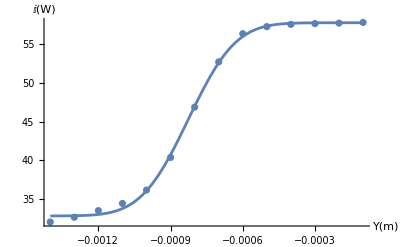

```mathematica
(*1.5 point*)
JumpDistance15=100*^-6;
z15=0.2*^-3+0.00000000000000000000000000001;
IIm1={57.86,57.77,57.71,57.61,57.32,56.4,52.74,46.87,40.34,36.11,34.37,33.44,32.58,31.96};
direction=Sign[IIm1[[1]]-IIm1[[Length[IIm1]]]];
Ym1=Range[Length[IIm1]]*JumpDistance15;
Data1=Table[0,{i,2},{j,Length[IIm1]}];
Data1[[1]]=-Ym1;
Data1[[2]]=IIm1;
model=1/4 π α w^2 ( direction*erf((√2 (Y-Y0))/w)+1)+BG;
{αGuess,wGuess,Y0Guess,BGGuess}={10*(0.3/0.5)^2/(0.001^2*1/4 π),0.001,0.00002,Min[IIm1]}
modelGuess=1/4 π αGuess wGuess^2 ( direction*erf((√2 (Y-Y0Guess))/wGuess)+1)+BGGuess;
fit1=FindFit[Transpose[Data1],model,{{α,αGuess},{w,wGuess},{Y0,Y0Guess},{BG,BGGuess}},Y]
{α15,w15,Y015}={α,w,Y0}/.fit1;
Show[Plot[{model/.fit1},{Y,-Ym1[[1]],-Ym1[[Length[IIm1]]]},PlotRange->All,AxesLabel->{Y[m],I[W]}],ListPlot[Transpose[Data1],AxesLabel->{Y[m],I[W]}]]
```

```mathematica
(*2nd point*)
```

0.0006

{1.3751×10^8,0.0001,-0.00019,30.81}

{α→1.90794×10^8,w→0.000293486,Y0→-0.000726856,BG→32.121}

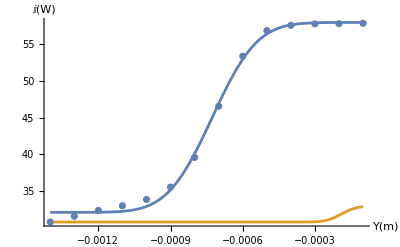

```mathematica
JumpDistance2=100*^-6;
z2=0.6*^-3+0.00000000000000000000000000001
IIm1={57.82,57.77,57.74,57.54,56.82,53.35,46.55,39.59,35.56,33.87,33.02,32.39,31.59,30.81};
direction=Sign[IIm1[[1]]-IIm1[[Length[IIm1]]]];
Ym1=Range[Length[IIm1]]*JumpDistance2;
Data1=Table[0,{i,2},{j,Length[IIm1]}];
Data1[[1]]=-Ym1;
Data1[[2]]=IIm1;
model=1/4 π α w^2 ( direction*erf((√2 (Y-Y0))/w)+1)+BG;
{αGuess,wGuess,Y0Guess,BGGuess}={3*(0.3/0.5)^2/(0.0001^2*1/4 π),0.0001,-0.00019,Min[IIm1]}
modelGuess=1/4 π αGuess wGuess^2 ( direction*erf((√2 (Y-Y0Guess))/wGuess)+1)+BGGuess;
fit1=FindFit[Transpose[Data1],model,{{α,αGuess},{w,wGuess},{Y0,Y0Guess},{BG,BGGuess}},Y]
{α2,w2,Y02}={α,w,Y0}/.fit1;
Show[Plot[{model/.fit1,modelGuess},{Y,-Ym1[[1]],-Ym1[[Length[IIm1]]]},PlotRange->All,AxesLabel->{Y[m],I[W]}],ListPlot[Transpose[Data1],AxesLabel->{Y[m],I[W]}]]
```

```mathematica
(*3rd Point*)
```

0.0012

{5.50039×10^6,0.0005,-0.00019,30.28}

{α→1.9408×10^8,w→0.000296855,Y0→-0.000533221,BG→31.3205}

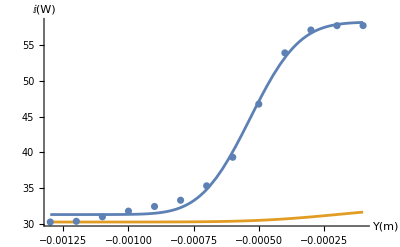

```mathematica
JumpDistance3=100*^-6;
z3=1.2*^-3+0.00000000000000000000000000001
IIm1={57.7,57.69,57.08,53.89,46.74,39.32,35.33,33.32,32.45,31.8,31.01,30.38,30.28};
direction=Sign[IIm1[[1]]-IIm1[[Length[IIm1]]]];
Ym1=Range[Length[IIm1]]*JumpDistance3;
Data1=Table[0,{i,2},{j,Length[IIm1]}];
Data1[[1]]=-Ym1;
Data1[[2]]=IIm1;
model=1/4 π α w^2 ( direction*erf((√2 (Y-Y0))/w)+1)+BG;
{αGuess,wGuess,Y0Guess,BGGuess}={3*(0.3/0.5)^2/(0.0005^2*1/4 π),0.0005,-0.00019,Min[IIm1]}
modelGuess=1/4 π αGuess wGuess^2 ( direction*erf((√2 (Y-Y0Guess))/wGuess)+1)+BGGuess;
fit1=FindFit[Transpose[Data1],model,{{α,αGuess},{w,wGuess},{Y0,Y0Guess},{BG,BGGuess}},Y]
{α3,w3,Y03}={α,w,Y0}/.fit1;
Show[Plot[{model/.fit1,modelGuess},{Y,-Ym1[[1]],-Ym1[[Length[IIm1]]]},PlotRange->All,AxesLabel->{Y[m],I[W]}],ListPlot[Transpose[Data1],AxesLabel->{Y[m],I[W]}]]
```

0.0018

{5.50039×10^6,0.0005,-0.00019,30.35}

{α→1.53496×10^8,w→0.000337859,Y0→-0.000433957,BG→31.0472}

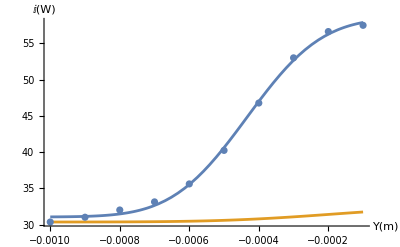

```mathematica
(*4rd Point*)
JumpDistance4=100*^-6;
z4=1.8*^-3+0.00000000000000000000000000001
IIm1={57.51,56.65,53.02,46.78,40.24,35.61,33.13,32.01,31.01,30.35};
direction=Sign[IIm1[[1]]-IIm1[[Length[IIm1]]]];
Ym1=Range[Length[IIm1]]*JumpDistance4;
Data1=Table[0,{i,2},{j,Length[IIm1]}];
Data1[[1]]=-Ym1;
Data1[[2]]=IIm1;
model=1/4 π α w^2 ( direction*erf((√2 (Y-Y0))/w)+1)+BG;
{αGuess,wGuess,Y0Guess,BGGuess}={3*(0.3/0.5)^2/(0.0005^2*1/4 π),0.0005,-0.00019,Min[IIm1]}
modelGuess=1/4 π αGuess wGuess^2 ( direction*erf((√2 (Y-Y0Guess))/wGuess)+1)+BGGuess;
fit1=FindFit[Transpose[Data1],model,{{α,αGuess},{w,wGuess},{Y0,Y0Guess},{BG,BGGuess}},Y]
{α4,w4,Y04}={α,w,Y0}/.fit1;
Show[Plot[{model/.fit1,modelGuess},{Y,-Ym1[[1]],-Ym1[[Length[IIm1]]]},PlotRange->All,AxesLabel->{Y[m],I[W]}],ListPlot[Transpose[Data1],AxesLabel->{Y[m],I[W]}]]
```

0.0024

{5.50039×10^6,0.0005,-0.00019,30.45}

{α→1.15587×10^8,w→0.00039172,Y0→-0.000537479,BG→30.5424}

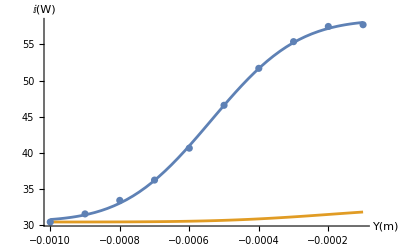

```mathematica
JumpDistance5=100*^-6;
z5=2.4*^-3+0.00000000000000000000000000001
IIm1={57.73,57.49,55.39,51.7,46.59,40.66,36.25,33.44,31.57,30.45};
direction=Sign[IIm1[[1]]-IIm1[[Length[IIm1]]]];
Ym1=Range[Length[IIm1]]*JumpDistance5;
Data1=Table[0,{i,2},{j,Length[IIm1]}];
Data1[[1]]=-Ym1;
Data1[[2]]=IIm1;
model=1/4 π α w^2 ( direction*erf((√2 (Y-Y0))/w)+1)+BG;
{αGuess,wGuess,Y0Guess,BGGuess}={3*(0.3/0.5)^2/(0.0005^2*1/4 π),0.0005,-0.00019,Min[IIm1]}
modelGuess=1/4 π αGuess wGuess^2 ( direction*erf((√2 (Y-Y0Guess))/wGuess)+1)+BGGuess;
fit1=FindFit[Transpose[Data1],model,{{α,αGuess},{w,wGuess},{Y0,Y0Guess},{BG,BGGuess}},Y]
{α5,w5,Y05}={α,w,Y0}/.fit1;
Show[Plot[{model/.fit1,modelGuess},{Y,-Ym1[[1]],-Ym1[[Length[IIm1]]]},PlotRange->All,AxesLabel->{Y[m],I[W]}],ListPlot[Transpose[Data1],AxesLabel->{Y[m],I[W]}]]
```

0.003

{5.50039×10^6,0.0005,-0.00019,30.55}

{α→7.42597×10^7,w→0.000498932,Y0→-0.000535745,BG→30.0861}

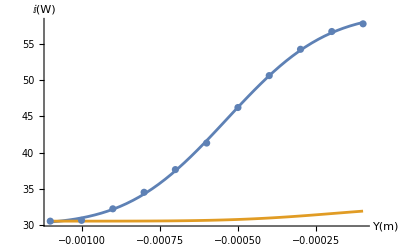

```mathematica
JumpDistance6=100*^-6;
z6=3*^-3+0.00000000000000000000000000001
IIm1={57.76,56.7,54.25,50.62,46.22,41.32,37.66,34.53,32.25,30.66,30.55};
direction=Sign[IIm1[[1]]-IIm1[[Length[IIm1]]]];
Ym1=Range[Length[IIm1]]*JumpDistance6;
Data1=Table[0,{i,2},{j,Length[IIm1]}];
Data1[[1]]=-Ym1;
Data1[[2]]=IIm1;
model=1/4 π α w^2 ( direction*erf((√2 (Y-Y0))/w)+1)+BG;
{αGuess,wGuess,Y0Guess,BGGuess}={3*(0.3/0.5)^2/(0.0005^2*1/4 π),0.0005,-0.00019,Min[IIm1]}
modelGuess=1/4 π αGuess wGuess^2 ( direction*erf((√2 (Y-Y0Guess))/wGuess)+1)+BGGuess;
fit1=FindFit[Transpose[Data1],model,{{α,αGuess},{w,wGuess},{Y0,Y0Guess},{BG,BGGuess}},Y]
{α6,w6,Y06}={α,w,Y0}/.fit1;
Show[Plot[{model/.fit1,modelGuess},{Y,-Ym1[[1]],-Ym1[[Length[IIm1]]]},PlotRange->All,AxesLabel->{Y[m],I[W]}],ListPlot[Transpose[Data1],AxesLabel->{Y[m],I[W]}]]
```

0.0036

{5.50039×10^6,0.0005,-0.00019,30.77}

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{α→4.9783×10^7,w→0.000608038,Y0→-0.000741946,BG→29.9187}

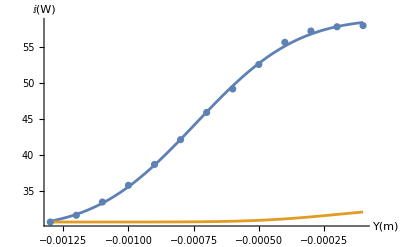

```mathematica
JumpDistance7=100*^-6;
z7=3.6*^-3+0.00000000000000000000000000001
IIm1={57.89,57.73,57.14,55.58,52.52,49.14,45.9,42.14,38.72,35.84,33.53,31.7,30.77};
direction=Sign[IIm1[[1]]-IIm1[[Length[IIm1]]]];
Ym1=Range[Length[IIm1]]*JumpDistance7;
Data1=Table[0,{i,2},{j,Length[IIm1]}];
Data1[[1]]=-Ym1;
Data1[[2]]=IIm1;
model=1/4 π α w^2 ( direction*erf((√2 (Y-Y0))/w)+1)+BG;
{αGuess,wGuess,Y0Guess,BGGuess}={3*(0.3/0.5)^2/(0.0005^2*1/4 π),0.0005,-0.00019,Min[IIm1]}
modelGuess=1/4 π αGuess wGuess^2 ( direction*erf((√2 (Y-Y0Guess))/wGuess)+1)+BGGuess;
fit1=FindFit[Transpose[Data1],model,{{α,αGuess},{w,wGuess},{Y0,Y0Guess},{BG,BGGuess}},Y]
{α7,w7,Y07}={α,w,Y0}/.fit1;
Show[Plot[{model/.fit1,modelGuess},{Y,-Ym1[[1]],-Ym1[[Length[IIm1]]]},PlotRange->All,AxesLabel->{Y[m],I[W]}],ListPlot[Transpose[Data1],AxesLabel->{Y[m],I[W]}]]
```

0.0042

{5.50039×10^6,0.0005,-0.00019,31.03}

{α→2.85106×10^7,w→0.000846375,Y0→-0.00061535,BG→29.2032}

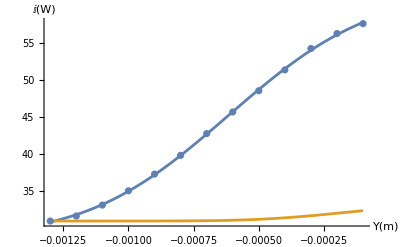

```mathematica
JumpDistance8=100*^-6;
z8=4.2*^-3+0.00000000000000000000000000001
IIm1={57.54,56.21,54.2,51.33,48.53,45.68,42.77,39.85,37.33,35.09,33.17,31.71,31.03};
direction=Sign[IIm1[[1]]-IIm1[[Length[IIm1]]]];
Ym1=Range[Length[IIm1]]*JumpDistance8;
Data1=Table[0,{i,2},{j,Length[IIm1]}];
Data1[[1]]=-Ym1;
Data1[[2]]=IIm1;
model=1/4 π α w^2 ( direction*erf((√2 (Y-Y0))/w)+1)+BG;
{αGuess,wGuess,Y0Guess,BGGuess}={3*(0.3/0.5)^2/(0.0005^2*1/4 π),0.0005,-0.00019,Min[IIm1]}
modelGuess=1/4 π αGuess wGuess^2 ( direction*erf((√2 (Y-Y0Guess))/wGuess)+1)+BGGuess;
fit1=FindFit[Transpose[Data1],model,{{α,αGuess},{w,wGuess},{Y0,Y0Guess},{BG,BGGuess}},Y]
{α8,w8,Y08}={α,w,Y0}/.fit1;
Show[Plot[{model/.fit1,modelGuess},{Y,-Ym1[[1]],-Ym1[[Length[IIm1]]]},PlotRange->All,AxesLabel->{Y[m],I[W]}],ListPlot[Transpose[Data1],AxesLabel->{Y[m],I[W]}]]
```

Once we have measured the waist at multiple points, we can fit it to the beam profile to try to find the absolute waist
Equation of a focused beam waist profile: w(z)= w0*√(1+((z-z0)/z_R)^2)=w0*√(1+((z-z0)/(π*w0^2)/λ)^2) 
Where w0 is the absolute waist, z-z0 is the distance from the waist to the measurement point and λ is the wavelength

{0.000319267,0.000293486,0.000296855,0.000337859,0.00039172,0.000498932,0.000608038,0.000846375}

{1.×10^-29,0.0006,0.0012,0.0018,0.0024,0.003,0.0036,0.0042}

{0.0003,0.001}

{w0→7.20524×10^-7,z0→-0.00172144}

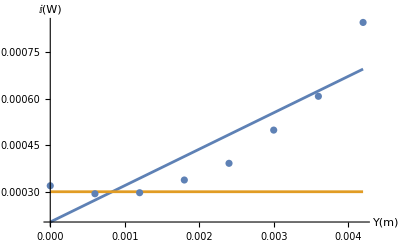

```mathematica
(*Fit points to beam profile*)
IIm1={w1,w2,w3,w4,w5,w6,w7,w8}
Ym1={z1,z2,z3,z4,z5,z6,z7,z8}
Data1=Table[0,{i,2},{j,Length[IIm1]}];
Data1[[1]]=Ym1;
Data1[[2]]=IIm1;
model=w0*√(1+((z-z0)/(π*w0^2)/λ)^2);
{w0Guess,z0Guess}={0.0003,0.001}
modelGuess=w0Guess*√(1+((z-z0Guess)/zR[λ,w0Guess])^2);
fit1=FindFit[Transpose[Data1],model,{{w0,w0Guess},{z0,z0Guess}},z]
{w01,z01}={w0,z0}/.fit1;
Show[Plot[{model/.fit1,modelGuess},{z,Ym1[[1]],Ym1[[Length[IIm1]]]},PlotRange->All,AxesLabel->{Y[m],I[W]}],ListPlot[Transpose[Data1],AxesLabel->{z[m],w[m]}]]
```